```mathematica
f[x_]=Cos[x^2]
```

Cos[x^2]

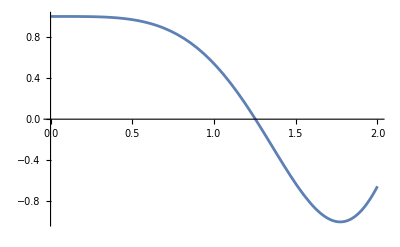

```mathematica
Plot[f[x],{x,0,2}]
```

Integral definida de f(x) con la Regla de Simpson
Para N = 4

```mathematica
I4=1./12(f[0]+4f[1/4]+2f[1/2]+4f[3/4]+2f[1]+4f[5/4]+2f[3/2]+4f[7/4]+f[2])
```

0.460835

Para N = 8

```mathematica
I8=1./24(f[0]+4f[1/8]+2f[1/4]+4f[3/8]+2f[1/2]+4f[5/8]+2f[3/4]+4f[7/8]+2f[1]+4f[9/8]+2f[5/4]+4f[11/8]+2f[3/2]+4f[13/8]+2f[7/4]+4f[15/8]+f[2])
```

0.461418

Para N = 16

```mathematica
I16=1./48(f[0]+2f[1/8]+2f[1/4]+2f[3/8]+2f[1/2]+2f[5/8]+2f[3/4]+2f[7/8]+2f[1]+2f[9/8]+2f[5/4]+2f[11/8]+2f[3/2]+2f[13/8]+2f[7/4]+2f[15/8]+f[2]+4*(f[1/16]+f[3/16]+f[5/16]+f[7/16]+f[9/16]+f[11/16]+f[13/16]+f[15/16]+f[17/16]+f[19/16]+f[21/16]+f[23/16]+f[25/16]+f[27/16]+f[29/16]+f[31/16]))
```

0.461459